```mathematica
S[t_,x_]:=Exp[σ Sqrt[t]x-σ^2/2 t]
```

```mathematica
$Assumptions=A>0
```

A>0

```mathematica
s=Expectation[Abs[Exp[x]-Exp[A]],x\[Distributed]NormalDistribution[0,σ Sqrt[t]]]
```

1/2 (ⅇ^A-ⅇ^((t σ^2)/2)+ⅇ^A Erf[A/(√2 √t σ)]-ⅇ^((t σ^2)/2) Erf[(A-t σ^2)/(√2 √t σ)]-ⅇ^A Erfc[A/(√2 √t σ)]+ⅇ^((t σ^2)/2) Erfc[(A-t σ^2)/(√2 √t σ)])

```mathematica
Simplify[Expand[s/Exp[A]/.A->σ^2 t/2]]
```

1/2 (2 Erf[(√t σ)/(2 √2)]+Erfc[-(√t σ)/(2 √2)]-Erfc[(√t σ)/(2 √2)])

```mathematica
(*it holds*)Erf[t]=1-Erfc[t];Erfc[A]==2-Erfc[-A];
```

```mathematica
1/2 (2+2-4Erfc[(√t σ)/(2 √2)])
```

```mathematica
CDF[NormalDistribution[0,1]]
```

1/2 Erfc[(0-#1)/(√2 1)]&

```mathematica
Expectation[(S[t,x]-1)^2,x\[Distributed]NormalDistribution[]]
```

-1+ⅇ^(t σ^2)

```mathematica
Expectation[Abs[x-1],x\[Distributed]NormalDistribution[0,Sqrt[t]]]
```

Expectation[Abs[x σ-(t σ^2)/2],x\[Distributed]NormalDistribution[0,√t]]

```mathematica
f[x_]:=Sin[x]+1
```

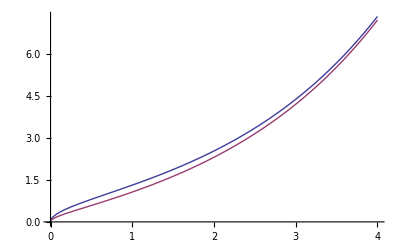

```mathematica
Plot[{Sqrt[Exp[t]-1],Sqrt[Exp[t]-1-(2(1-Erfc[(√t)/(2 √2)]))^2]},{t,0,4}]
```

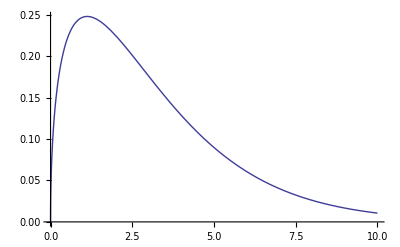

```mathematica
Plot[Sqrt[Exp[t]-1]-Sqrt[Exp[t]-1-(2(1-Erfc[(√t)/(2 √2)]))^2],{t,0,10}]
```

```mathematica
s=.
```

```mathematica
Eigenvalues[{{s^2,-s},{-s,1}}]
```

{0,1+s^2}

```mathematica
Inverse[{{-a,1},{-b,a}}]
```

{{a/(-a^2+b),-1/(-a^2+b)},{b/(-a^2+b),-a/(-a^2+b)}}

```mathematica
D[Sqrt[x],{x,2}]
```

-1/(4 x^(3/2))